```mathematica
Clear["Global`*"]
```

```mathematica
(*定义常微分方程组*)
eqns={
-c *U[x]-q *U[x]^3+(3/2) q *U[x] V[x]-(q/4)* U''[x] ,
-c *V[x]+(3/4) q* V[x]^2-3 q *U[x]^2 V[x]+(3 q/4)* (U'[x])^2+(3 q/2) *U[x] U''[x]-(1/4) q *V''[x] 
}/.{U-> Function[x,Subscript[a, 0] +Subscript[a, 1]*P[x]+Subscript[b, 1]*P[x]^(-1)], V-> Function[x,Subscript[c, 0] +Subscript[c, 1]*P[x]+Subscript[c, 2]*P[x]^2+Subscript[d, 1]*P[x]^(-1)+Subscript[d, 2]*P[x]^(-2)]};
```

```mathematica
Clear[Subscript[r, 0],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]]
```

情况4
参考文献：Analytical soliton solutions for cubic-quartic perturbations of the Lakshmanan-Porsezian-Daniel equation using the modified extended tanh function method (have typo!)

Optical soliton perturbation with Kudryashov’s generalized law of refractive index and generalized nonlocal laws by improved modified extended tanh method

约束方程：

```mathematica
(*情况1(无解)： r0=r1=r3=0; *)
(*情况2(有解)： r0=r2^2/(4*r4);r1=r3=0; *)
(*情况3(无解)： r0=r1=r2=0; *)
(*情况4(有解，复杂)： r0=r1=0; *)
(*情况5(有解)： r1=r3=0; *)
 Subscript[r, 0]=Subscript[r, 1]=0;
SubEqns = eqns/.{P'[x] ->Sqrt[Subscript[r, 0]+Subscript[r, 1]*P[x]+Subscript[r, 2]*P[x]^2+Subscript[r, 3]*P[x]^3 + Subscript[r, 4]*P[x]^4 ]}/.{P''[x]->(1/2)*(Subscript[r, 1] + 2*Subscript[r, 2]*P[x] + 3*Subscript[r, 3]*P[x]^2 + 4*Subscript[r, 4]*P[x]^3)}/.{P[x]->P}
```

{-c (a_0+P a_1+b_1/P)-q (a_0+P a_1+b_1/P)^3+3/2 q (a_0+P a_1+b_1/P) (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)-1/4 q (1/2 a_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4)-(b_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4))/(2 P^2)+(2 b_1 (P^2 r_2+P^3 r_3+P^4 r_4))/P^3),-c (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)-3 q (a_0+P a_1+b_1/P)^2 (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)+3/4 q (c_0+P c_1+P^2 c_2+d_1/P+d_2/P^2)^2+3/4 q (a_1 √(P^2 r_2+P^3 r_3+P^4 r_4)-(b_1 √(P^2 r_2+P^3 r_3+P^4 r_4))/P^2)^2+3/2 q (a_0+P a_1+b_1/P) (1/2 a_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4)-(b_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4))/(2 P^2)+(2 b_1 (P^2 r_2+P^3 r_3+P^4 r_4))/P^3)-1/4 q (1/2 c_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4)+P c_2 (2 P r_2+3 P^2 r_3+4 P^3 r_4)-(d_1 (2 P r_2+3 P^2 r_3+4 P^3 r_4))/(2 P^2)-(d_2 (2 P r_2+3 P^2 r_3+4 P^3 r_4))/P^3+2 c_2 (P^2 r_2+P^3 r_3+P^4 r_4)+(2 d_1 (P^2 r_2+P^3 r_3+P^4 r_4))/P^3+(6 d_2 (P^2 r_2+P^3 r_3+P^4 r_4))/P^4)}

```mathematica
(*每一项乘上P四次方，变为正次的多项式*)
expandedEqns=Expand[SubEqns*P^4];
(* P 的各个次幂*)
coeffEqns=Flatten[CoefficientList[expandedEqns,P]];
(*列出方程组*)
eqnList=Thread[coeffEqns==0];
```

方程组展示

```mathematica
Exponent[expandedEqns,P]
eqnShow = # ==0&/@coeffEqns /.P->ϕ;
allP=Join[Table[Inactivate[ϕ^n,Power],{n,0,7}],Table[Inactivate[ϕ^n,Power],{n,0,8}]];
Grid[Transpose[{allP,eqnShow }]]
```

{7,8}

ϕ^0 | True
ϕ^1 | -q b_1^3+3/2 q b_1 d_2==0
ϕ^2 | -3 q a_0 b_1^2+3/2 q b_1 d_1+3/2 q a_0 d_2==0
ϕ^3 | -c b_1-3 q a_0^2 b_1-3 q a_1 b_1^2+3/2 q b_1 c_0+3/2 q a_0 d_1+3/2 q a_1 d_2-1/4 q b_1 r_2==0
ϕ^4 | -c a_0-q a_0^3-6 q a_0 a_1 b_1+3/2 q a_0 c_0+3/2 q b_1 c_1+3/2 q a_1 d_1-1/8 q b_1 r_3==0
ϕ^5 | -c a_1-3 q a_0^2 a_1-3 q a_1^2 b_1+3/2 q a_1 c_0+3/2 q a_0 c_1+3/2 q b_1 c_2-1/4 q a_1 r_2==0
ϕ^6 | -3 q a_0 a_1^2+3/2 q a_1 c_1+3/2 q a_0 c_2-3/8 q a_1 r_3==0
ϕ^7 | -q a_1^3+3/2 q a_1 c_2-1/2 q a_1 r_4==0
ϕ^0 | -3 q b_1^2 d_2+(3 q d_2^2)/4==0
ϕ^1 | -3 q b_1^2 d_1-6 q a_0 b_1 d_2+3/2 q d_1 d_2==0
ϕ^2 | -3 q b_1^2 c_0-6 q a_0 b_1 d_1+(3 q d_1^2)/4-c d_2-3 q a_0^2 d_2-6 q a_1 b_1 d_2+3/2 q c_0 d_2+9/4 q b_1^2 r_2-q d_2 r_2==0
ϕ^3 | -6 q a_0 b_1 c_0-3 q b_1^2 c_1-c d_1-3 q a_0^2 d_1-6 q a_1 b_1 d_1+3/2 q c_0 d_1-6 q a_0 a_1 d_2+3/2 q c_1 d_2+3/2 q a_0 b_1 r_2-1/4 q d_1 r_2+3/2 q b_1^2 r_3-3/4 q d_2 r_3==0
ϕ^4 | -c c_0-3 q a_0^2 c_0-6 q a_1 b_1 c_0+(3 q c_0^2)/4-6 q a_0 b_1 c_1-3 q b_1^2 c_2-6 q a_0 a_1 d_1+3/2 q c_1 d_1-3 q a_1^2 d_2+3/2 q c_2 d_2+3/2 q a_1 b_1 r_2+3/4 q a_0 b_1 r_3-1/8 q d_1 r_3+3/4 q b_1^2 r_4-1/2 q d_2 r_4==0
ϕ^5 | -6 q a_0 a_1 c_0-c c_1-3 q a_0^2 c_1-6 q a_1 b_1 c_1+3/2 q c_0 c_1-6 q a_0 b_1 c_2-3 q a_1^2 d_1+3/2 q c_2 d_1+3/2 q a_0 a_1 r_2-1/4 q c_1 r_2+3/2 q a_1 b_1 r_3==0
ϕ^6 | -3 q a_1^2 c_0-6 q a_0 a_1 c_1+(3 q c_1^2)/4-c c_2-3 q a_0^2 c_2-6 q a_1 b_1 c_2+3/2 q c_0 c_2+9/4 q a_1^2 r_2-q c_2 r_2+9/4 q a_0 a_1 r_3-3/8 q c_1 r_3+3/2 q a_1 b_1 r_4==0
ϕ^7 | -3 q a_1^2 c_1-6 q a_0 a_1 c_2+3/2 q c_1 c_2+3 q a_1^2 r_3-5/4 q c_2 r_3+3 q a_0 a_1 r_4-1/2 q c_1 r_4==0
ϕ^8 | -3 q a_1^2 c_2+(3 q c_2^2)/4+15/4 q a_1^2 r_4-3/2 q c_2 r_4==0

```mathematica
(*约束条件为：如果这几项全部都为零就排除，不显示 ,AnyTrue[{Subscript[a, 1],Subscript[b, 1],Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2]},#!=0&]*)
addConstraints={q!=0,Not[(Subscript[a, 1]==0&&Subscript[b, 1]==0)||(Subscript[c, 1]==0&&Subscript[c, 2]==0&&Subscript[d, 1]==0&&Subscript[d, 2]==0)]};
solutions=Solve[Join[eqnList,addConstraints],{Subscript[r, 2],Subscript[r, 3],Subscript[r, 4],Subscript[a, 0],Subscript[a, 1],Subscript[b, 1],Subscript[c, 0],Subscript[c, 1],Subscript[c, 2],Subscript[d, 1],Subscript[d, 2]}];
solutions//Column
```

Solve::svars: 方程可能无法给出所有 " solve " 变量的解.

{r_2→-(4 c)/q,r_3→-(8 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→0,c_1→-(2 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(4 c)/q,r_3→(8 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→0,c_1→(2 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 c)/q,r_3→-(8 ⅈ √c a_1)/(√3 √q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→(4 c)/(3 q),c_1→-(2 ⅈ √c a_1)/(√3 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 c)/q,r_3→(8 ⅈ √c a_1)/(√3 √q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→(4 c)/(3 q),c_1→(2 ⅈ √c a_1)/(√3 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(4 c)/q,r_3→-(4 ⅈ √c a_1)/(√q),r_4→a_1^2,a_0→-(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→-(2 ⅈ √c a_1)/(√q),c_2→a_1^2,d_1→0,d_2→0}
{r_2→-(4 c)/q,r_3→-(8 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→-(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→-(2 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(16 c)/q,r_3→-(16 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→-(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→-(4 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(4 c)/q,r_3→(4 ⅈ √c a_1)/(√q),r_4→a_1^2,a_0→(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→(2 ⅈ √c a_1)/(√q),c_2→a_1^2,d_1→0,d_2→0}
{r_2→-(4 c)/q,r_3→(8 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→(2 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(16 c)/q,r_3→(16 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→(ⅈ √c)/(√q),b_1→0,c_0→0,c_1→(4 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 (-(15 √5 c)/(√q)+(7 √21 c)/(√q)))/(9 √5 √q-5 √21 √q),r_3→(4 ⅈ (-9 √5+5 √21) √c a_1)/(15 √q),r_4→4 a_1^2,a_0→-(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→-(ⅈ (9 √5 √c a_1-5 √21 √c a_1))/(15 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 (-(15 √5 c)/(√q)-(7 √21 c)/(√q)))/(9 √5 √q+5 √21 √q),r_3→-(4 ⅈ (9 √5+5 √21) √c a_1)/(15 √q),r_4→4 a_1^2,a_0→-(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→-(ⅈ (9 √5 √c a_1+5 √21 √c a_1))/(15 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 (-(15 √5 c)/(√q)+(7 √21 c)/(√q)))/(9 √5 √q-5 √21 √q),r_3→-(4 ⅈ (-9 √5+5 √21) √c a_1)/(15 √q),r_4→4 a_1^2,a_0→(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→(ⅈ (9 √5 √c a_1-5 √21 √c a_1))/(15 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 (-(15 √5 c)/(√q)-(7 √21 c)/(√q)))/(9 √5 √q+5 √21 √q),r_3→(4 ⅈ (9 √5+5 √21) √c a_1)/(15 √q),r_4→4 a_1^2,a_0→(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→(ⅈ (9 √5 √c a_1+5 √21 √c a_1))/(15 √q),c_2→2 a_1^2,d_1→0,d_2→0}

```mathematica
(*DeleteCases[solutionsRaw,_?(ContainsAll[#,{a0->0,a1->0,b1->0}]&)] ;*)
(*通过对solutions观察，我们需要把后面几项扔了*)
(*Map[DeleteCases[#,a0->0|a1->0|b1->0]&,solutionsRaw] 不行*)
```

从结果上看，两组情况都会涉及到,需要a1,c不等于零
-Graphics-

```mathematica
(*Map[Assuming[a1!=0,(r3^2==4*r2*r4)/.#]&,solutions]*)
mark=Map[Refine[(Subscript[r, 3]^2==4*Subscript[r, 2]*Subscript[r, 4])/.#,{Subscript[a, 1]!=0,c!=0}]&,solutions];
solutions1 = Pick[#,mark,True]&@solutions;
solutions2 = Pick[#,mark,False]&@solutions;
(*solutions1//Column
solutions2//Column*)
solNice1=solutions1[[1]];
solNice2=solutions2[[{1,4}]]//FullSimplify;
solNice2=solNice2/.(9 √5+5 √21)->15*Subscript[k, 1];
solNiceC ={solNice1}~Join~solNice2;
solNiceC//Column
```

{r_2→-(4 c)/q,r_3→-(8 ⅈ √c a_1)/(√q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→0,c_1→-(2 ⅈ √c a_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→(4 c)/q,r_3→-(8 ⅈ √c a_1)/(√3 √q),r_4→4 a_1^2,a_0→0,b_1→0,c_0→(4 c)/(3 q),c_1→-(2 ⅈ √c a_1)/(√3 √q),c_2→2 a_1^2,d_1→0,d_2→0}
{r_2→-(2 (5+√105) c)/(5 q),r_3→-(4 ⅈ √c a_1 k_1)/(√q),r_4→4 a_1^2,a_0→-(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→-(ⅈ √c a_1 k_1)/(√q),c_2→2 a_1^2,d_1→0,d_2→0}

```mathematica
solNice=Map[Append[#,Subscript[a, 1]->1]&,solNiceC/.Subscript[a, 1]->1];
solNice//Column
```

{r_2→-(4 c)/q,r_3→-(8 ⅈ √c)/(√q),r_4→4,a_0→0,b_1→0,c_0→0,c_1→-(2 ⅈ √c)/(√q),c_2→2,d_1→0,d_2→0,a_1→1}
{r_2→(4 c)/q,r_3→-(8 ⅈ √c)/(√3 √q),r_4→4,a_0→0,b_1→0,c_0→(4 c)/(3 q),c_1→-(2 ⅈ √c)/(√3 √q),c_2→2,d_1→0,d_2→0,a_1→1}
{r_2→-(2 (5+√105) c)/(5 q),r_3→-(4 ⅈ √c k_1)/(√q),r_4→4,a_0→-(ⅈ √c)/(√5 √q),b_1→0,c_0→(8 c)/(15 q),c_1→-(ⅈ √c k_1)/(√q),c_2→2,d_1→0,d_2→0,a_1→1}

两组中只用其中一种情况，另一个类似，但是第二组需要有另一种情况，不讨论了，太多了

```mathematica
(*最简单情况，c，q都大于零*)
Clear[v,u]
```

约束方程解的处理 c>0, q<0

```mathematica
odeList =P[z]->(-Subscript[r, 2](Tanh[1/2*√Subscript[r, 2]*z]+1))/Subscript[r, 3]/.solNice1;
r2Pos = (Subscript[r, 2] Sech[1/2 √Subscript[r, 2]*z]^2)/(2 √(Subscript[r, 2]*Subscript[r, 4])Tanh[1/2 √Subscript[r, 2]*z]-Subscript[r, 3]);r2Neg =  -(Subscript[r, 2] Sec[1/2 √(-Subscript[r, 2])*z]^2)/(2 √(-Subscript[r, 2]*Subscript[r, 4])Tan[1/2 √(-Subscript[r, 2])*z]+Subscript[r, 3]);
odeList2 = Map[
If[
Simplify[Subscript[r, 2]>0/. #, c>0&&q <0],
P[z]->r2Pos/.#, P[z]-> r2Neg/.#]&,
solNice2
];

c1usol= Subscript[a, 0] +Subscript[a, 1]*P[z]+Subscript[b, 1]*P[z]^(-1)/.solNice1/. odeList/. z->(x-c*t);
c1vsol = Subscript[c, 0] +Subscript[c, 1]*P[z]+Subscript[c, 2]*P[z]^2+Subscript[d, 1]*P[z]^(-1)+Subscript[d, 2]*P[z]^(-2)/.solNice1/. odeList/. z->(x-c*t);
c2usol = MapThread[(Subscript[a, 0] +Subscript[a, 1]*P[z]+Subscript[b, 1]*P[z]^(-1)/. #1/. #2/. z->(x-c*t))&,{solNice2,odeList2}];
c2vsol = MapThread[(Subscript[c, 0] +Subscript[c, 1]*P[z]+Subscript[c, 2]*P[z]^2+Subscript[d, 1]*P[z]^(-1)+Subscript[d, 2]*P[z]^(-2)/. #1/. #2/. z->(x-c*t))&,{solNice2,odeList2}];
```

```mathematica
uNicer = {c1usol}~Join~c2usol/.Subscript[a, 1]->1/. 5+√105->Subscript[k, 2];
vNicer = {c1vsol}~Join~c2vsol/.Subscript[a, 1]->1/. 5+√105->Subscript[k, 2];
```

```mathematica
Grid[Transpose[{Subscript[r, 2]/.solNice,MapIndexed[Subscript[u, First[#2+38]]->#1&,uNicer],MapIndexed[Subscript[v, First[#2+38]]->#1&,vNicer]}]]
```

-(4 c)/q | u_39→(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q) | v_39→(c (1+Tanh[√(-c/q) (-c t+x)]))/q-(c (1+Tanh[√(-c/q) (-c t+x)])^2)/(2 q)
(4 c)/q | u_40→-(4 c Sec[√(-c/q) (-c t+x)]^2)/(q (-(8 ⅈ √c)/(√3 √q)+8 √(-c/q) Tan[√(-c/q) (-c t+x)])) | v_40→(4 c)/(3 q)+(32 c^2 Sec[√(-c/q) (-c t+x)]^4)/(q^2 (-(8 ⅈ √c)/(√3 √q)+8 √(-c/q) Tan[√(-c/q) (-c t+x)])^2)+(8 ⅈ c^(3/2) Sec[√(-c/q) (-c t+x)]^2)/(√3 q^(3/2) (-(8 ⅈ √c)/(√3 √q)+8 √(-c/q) Tan[√(-c/q) (-c t+x)]))
-(2 (5+√105) c)/(5 q) | u_41→-(ⅈ √c)/(√5 √q)-(2 c Sech[(√(-c/q) (-c t+x) √k_2)/(√10)]^2 k_2)/(5 q ((4 ⅈ √c k_1)/(√q)+4 √(2/5) √(-c/q) √k_2 Tanh[(√(-c/q) (-c t+x) √k_2)/(√10)])) | v_41→(8 c)/(15 q)+(8 c^2 Sech[(√(-c/q) (-c t+x) √k_2)/(√10)]^4 k_2^2)/(25 q^2 ((4 ⅈ √c k_1)/(√q)+4 √(2/5) √(-c/q) √k_2 Tanh[(√(-c/q) (-c t+x) √k_2)/(√10)])^2)+(2 ⅈ c^(3/2) Sech[(√(-c/q) (-c t+x) √k_2)/(√10)]^2 k_1 k_2)/(5 q^(3/2) ((4 ⅈ √c k_1)/(√q)+4 √(2/5) √(-c/q) √k_2 Tanh[(√(-c/q) (-c t+x) √k_2)/(√10)]))

为了r2>0,则c>0,q<0解形式差不多列一个

```mathematica
Grid[Transpose[{c2usol,c2vsol}]]
```

u→-(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])) | v→(4 c)/(3 q)+(32 a1^2 c^2 Sec[√(-c/q) (-c t+x)]^4)/(q^2 (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])^2)+(8 ⅈ a1 c^(3/2) Sec[√(-c/q) (-c t+x)]^2)/(√3 q^(3/2) (-(8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))
u→-(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])) | v→(4 c)/(3 q)+(32 a1^2 c^2 Sec[√(-c/q) (-c t+x)]^4)/(q^2 ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)])^2)-(8 ⅈ a1 c^(3/2) Sec[√(-c/q) (-c t+x)]^2)/(√3 q^(3/2) ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))
u→-(ⅈ √c)/(√5 √q)-(2 a1 (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (-5 c+√105 c)^2 Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])^2)+(2 ⅈ (9 √5 a1 √c-5 √21 a1 √c) (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) ((4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]))
u→-(ⅈ √c)/(√5 √q)-(2 a1 (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (5 c+√105 c)^2 Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])^2)+(2 ⅈ (9 √5 a1 √c+5 √21 a1 √c) (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) ((4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]))
u→(ⅈ √c)/(√5 √q)-(2 a1 (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (-5 c+√105 c)^2 Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)])^2)-(2 ⅈ (9 √5 a1 √c-5 √21 a1 √c) (-5 c+√105 c) Sec[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) (-(4 ⅈ (-9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (-5 c+√105 c))/q) Tan[(√(-(-5 c+√105 c)/q) (-c t+x))/(√10)]))
u→(ⅈ √c)/(√5 √q)-(2 a1 (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(5 q (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])) | v→(8 c)/(15 q)+(8 a1^2 (5 c+√105 c)^2 Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^4)/(25 q^2 (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)])^2)-(2 ⅈ (9 √5 a1 √c+5 √21 a1 √c) (5 c+√105 c) Sech[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]^2)/(75 q^(3/2) (-(4 ⅈ (9 √5+5 √21) a1 √c)/(15 √q)+4 √(2/5) √(-(a1^2 (5 c+√105 c))/q) Tanh[(√(-(5 c+√105 c)/q) (-c t+x))/(√10)]))

Singular solition solution -(4 a1 c Sec[√(-c/q) (-c t+x)]^2)/(q ((8 ⅈ a1 √c)/(√3 √q)+8 √(-(a1^2 c)/q) Tan[√(-c/q) (-c t+x)]))  c=2;q=-1;a1=1;
非连续 (ⅈ √c)/(√q)-(ⅈ √c (1+Tanh[2 √(-c/q) (-c t+x)]))/(√q) c=1;q=-30;a1 = 1; (调范围会出现奇点，没明白)

```mathematica
paraC=1;paraQ=-10;


setting1={ClippingStyle->None,
Exclusions->"Singularities",
ColorFunction->(ColorData["TemperatureMap"][#3]&),PlotPoints->70(* 60很顺滑*)
};
f[x_,t_]:=-(ⅈ √c)/(√5 √q)-(2 c Sech[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)]^2 Subscript[k, 2])/(5 q ((4 ⅈ √c Subscript[k, 1])/(√q)+4 √(2/5) √(-c/q) √Subscript[k, 2] Tanh[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)]))/. {q->paraQ,c->paraC,Subscript[k, 1]->(9 √5+5 √21)/15,Subscript[k, 2]->5+√105}
g[x_,t_]:=(8 c)/(15 q)+(8 c^2 Sech[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)]^4 Subscript[k, 2]^2)/(25 q^2 ((4 ⅈ √c Subscript[k, 1])/(√q)+4 √(2/5) √(-c/q) √Subscript[k, 2] Tanh[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)])^2)+(2 ⅈ c^(3/2) Sech[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)]^2 Subscript[k, 1] Subscript[k, 2])/(5 q^(3/2) ((4 ⅈ √c Subscript[k, 1])/(√q)+4 √(2/5) √(-c/q) √Subscript[k, 2] Tanh[(√(-c/q) (-c t+x) √Subscript[k, 2])/(√10)]))/. {q->paraQ,c->paraC,Subscript[k, 1]->(9 √5+5 √21)/15,Subscript[k, 2]->5+√105}
```

```mathematica
GraphicsRow[
{
Plot3D[f[x,t],{x,-10,10},{t,0,3},Evaluate[setting1],

AxesLabel->{"x","t","u_41"," "}],
Plot3D[g[x,t],{x,-10,10},{t,0,3},Evaluate[setting1],
AxesLabel->{"x","t","v_41"," "}]
},ImageSize->800]
```

-Graphics-

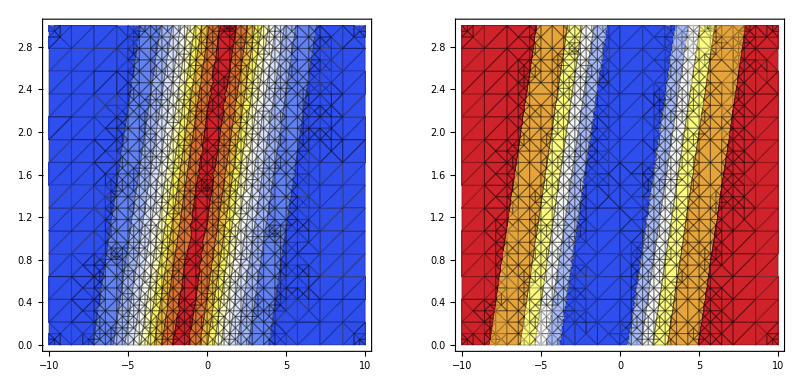

```mathematica
GraphicsRow[
{ContourPlot[f[x,t],{x,-10,10},{t,0,3},Mesh->All,
ColorFunction->"TemperatureMap"],
ContourPlot[g[x,t],{x,-10,10},{t,0,3},Mesh->All,
ColorFunction->"TemperatureMap"]},
ImageSize->800]
```

```mathematica
ft[x_,t_]:=(ⅈ √c (1+Tanh[√(-c/q) (-c t+x)]))/(2 √q)/. {q->paraQ,c->paraC,Subscript[k, 1]->(9 √5+5 √21)/15,Subscript[k, 2]->5+√105}
```

```mathematica
Plot3D[ft[x,t],{x,-10,10},{t,0,3},Evaluate[setting1],AxesLabel->{"x","t","U"," "},PlotLabel->"U"]
(*ContourPlot[Abs[f[x,t]],{x,-10,10},{t,0,3},Mesh->All,ColorFunction->"TemperatureMap"]*)
```

-Graphics3D-

```mathematica
Clear[q,c]
```

```mathematica
(*原始偏微分方程*)
Peqns={D[u[x,t],t]-3 q u[x,t]^2 D[u[x,t],x]+(3/2) q D[(u[x,t] v[x,t]),x]-(1/4) q D[u[x,t],{x,3}]==0,D[v[x,t],t]+(3/2) q v[x,t] D[v[x,t],x]-3 q D[(u[x,t]^2 v[x,t]),x]+3 q D[u[x,t],x] D[u[x,t],{x,2}]+(3/2) q u[x,t] D[u[x,t],{x,3}]-(1/4) q D[v[x,t],{x,3}]==0};
```

情况1的验证

```mathematica
Peqns/. 
{u->Function[{x,t},c1usol],
v->Function[{x,t},c1vsol]
}
```

{True,True}

```mathematica
Map[
(Peqns/. 
{u->Function[{x,t},c2usol[[#]]],
v->Function[{x,t},c2vsol[[#]]]
}
)&,{Table[i,{i,Length[c2usol]}]}
]
```

{{{0,0}==0,{0,0}==0}}